# Paper figures: p=3, q=3 pure simplicial complexes

Produces the four histogram panels for Figure 2 of the paper.
Run histograms_handoff_v2.nb first to generate all distributions,
then run this notebook to produce paper-ready figures.

## Paper Figure Style

```mathematica
(* Colors matching the paper *)
barColor  = RGBColor[0.984, 0.757, 0.369];  (* golden yellow *)
dotColor  = RGBColor[0.122, 0.471, 0.706];  (* muted blue    *)

(* Shared options *)
figOpts = Sequence[
  Frame       -> True,
  FrameStyle  -> Directive[Black, AbsoluteThickness[1]],
  FrameLabel  -> {
    {"Frequency", None},
    {"unlabeled 3-pure complex number (1-12)", None}
  },
  LabelStyle  -> Directive[FontFamily -> "Times", FontSize -> 11, Black],
  ImageSize   -> {360, 270},
  PlotRange   -> All,
  ImageMargins -> 5
];

(* Bar chart with no theory overlay *)
paperBarPlot[dist_List, ttl_String] :=
  BarChart[
    dist[[All, 2]],
    ChartStyle   -> barColor,
    ChartLabels  -> None,
    PlotLabel    -> Style[ttl, FontFamily -> "Times", FontSize -> 12, Bold],
    figOpts
  ];

(* Bar chart with theory dots overlay *)
paperBarVsTheoryPlot[dist_List, theoryDist_List, ttl_String] :=
  Show[
    BarChart[
      dist[[All, 2]],
      ChartStyle  -> barColor,
      ChartLabels -> None,
      figOpts
    ],
    ListPlot[
      theoryDist,
      PlotStyle   -> Directive[dotColor, AbsolutePointSize[7]],
      PlotMarkers -> {Graphics[{dotColor, Disk[]}], 0.05}
    ],
    PlotLabel -> Style[ttl, FontFamily -> "Times", FontSize -> 12, Bold],
    PlotRange -> All
  ];
```

## The Four Paper Plots

```mathematica
(* Panel 1: Unweighted *)
(* Bars = raw class frequencies from vertex-labeled sampler, no theory overlay. *)
fig1Unweighted = paperBarPlot[
  vertexEmpiricalDist,
  "Unweighted"
];
```

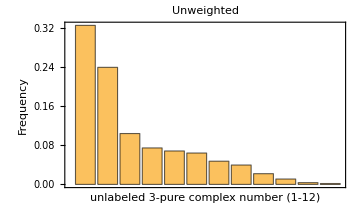

```mathematica
fig1Unweighted
```

```mathematica
(* Panel 2: Vertex-labeled *)
(* Bars = uniform vertex-labeled empirical; dots = n!/|Aut| theory (Eq. 20). *)
fig2VertexLabeled = paperBarVsTheoryPlot[
  vertexEmpiricalDist,
  vertexTheoryDist,
  "Vertex-labeled"
];
```

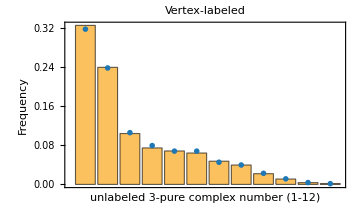

```mathematica
fig2VertexLabeled
```

```mathematica
(* Panel 3: Facet-labeled *)
(* Bars = vertex-labeled sample reweighted by w_f (Eq. 25); dots = q!/|Aut_F| theory (Eq. 22). *)
fig3FacetLabeled = paperBarVsTheoryPlot[
  weightedFacetDist,
  facetTheoryFormulaDist,
  "Facet-labeled"
];
```

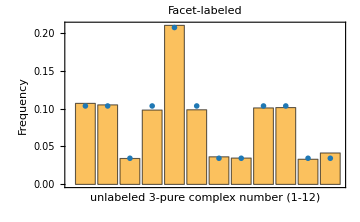

```mathematica
fig3FacetLabeled
```

```mathematica
(* Panel 4: Unlabeled *)
(* Bars = vertex-labeled sample reweighted by w_u (Eq. 24); dots = 1/12 uniform theory. *)
fig4Unlabeled = paperBarVsTheoryPlot[
  weightedUnlabeledDist,
  unlabeledTheoryDist,
  "Unlabeled"
];
```

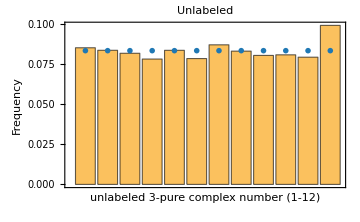

```mathematica
fig4Unlabeled
```

## Combined 2x2 Figure

```mathematica
fig2x2 = GraphicsGrid[
  {{fig1Unweighted, fig2VertexLabeled},
   {fig3FacetLabeled, fig4Unlabeled}},
  Spacings -> {0.3, 0.3},
  ImageSize -> 760
];
```

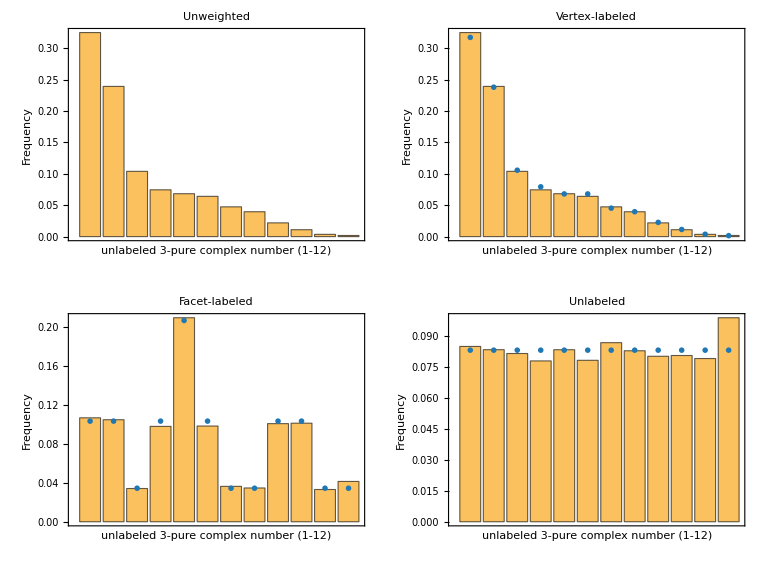

```mathematica
fig2x2
```

## Export

```mathematica
(* Individual PDFs *)
Export[baseName <> "_fig_unweighted.pdf",    fig1Unweighted];
Export[baseName <> "_fig_vertex_labeled.pdf", fig2VertexLabeled];
Export[baseName <> "_fig_facet_labeled.pdf",  fig3FacetLabeled];
Export[baseName <> "_fig_unlabeled.pdf",      fig4Unlabeled];

(* Combined 2x2 PDF for direct drop-in to paper *)
Export[baseName <> "_fig2_combined.pdf", fig2x2];

Print["Exported: ", baseName <> "_fig2_combined.pdf"];
Print["Exported: individual panel PDFs."];
```

Exported: p3q3_n10000_fig2_combined.pdf

Exported: individual panel PDFs.